# Dimère N = 2

### Initialisation

```mathematica
Get["http://nrgljubljana.ijs.si/sneg/sneg.m"]
Off[General::spell1];
snegfermionoperators[c]
snegrealconstants[ϵs,δd,J,U,𝒯,ϵ,𝒜,ℬ,𝒞,C1,C2,C3,C4,η,𝓉,ρ,𝒟,N20as,ℰ20as,N30as,N31as,N10as,N11as,ℰ22as,ℰ23as,N22as,N23as,ℰ21as,ℰ10as,ℰ11as,ℰ30as,ℰ31as,h,ℰ10,ℰ10p,ℰ11,ℰ11p,ℰ30,ℰ30p,ℰ31,ℰ31p,ℰ20,ℰ21p,ℰ21pp,ℰ21,ℰ22,ℰ23,ℰ24,S10,S11,S20,S30,S31,D02,Δv,t]

M=2;(*sites number*)Nel=2;(*electrons number*)ops=Table[c[i],{i,M}];
basis=makebasis[ops];
v=vacuum[];
MatrixForm[bz=qbasis[ops]];
MatrixForm[bvc=Map[{#[[1]],ap[#[[2]],v]}&,bz]];

bz;
bvc[[3,2]];
c[CR,1,UP];
c[AN,1,DO];
cr=Table[bz[[2,2,i]],{i,1,3,2}];
```

sneg 2.0.0 Copyright (C) 2002-2022 Rok Zitko

### Fonctions

```mathematica
cαψ[α_,s_,ψ_]:=nc[c[AN,α,s],ψ];
cβpψ[β_,s_,ψ_]:=nc[c[CR,β,s],ψ];
cβpcαψ[β_,α_,σ_,ψ_]:=nc[c[CR,β,σ],cαψ[α,σ,ψ]];
```

```mathematica
G1[ω,1,1,UP,Ket[ψ20as],ψ3as,ψ1as,ℰ3as,ℰ1as,ℰ20as,η]
```

```mathematica
G1[ω_,i_,j_,σ_,ψ_,LψNp1_,LψNm1_,ℰNp1_,ℰNm1_,e0_,η_]:=Module[{nmax,mmax,g1,g2,g3},
nmax = Length[LψNp1];
mmax = Length[LψNm1];
g1 = ∑_(n=1)^nmax ((nc[conj[LψNp1[[n]]],cβpψ[i,σ,ψ]]nc[conj[LψNp1[[n]]],cβpψ[j,σ,ψ]])/(ω-FullSimplify[ℰNp1[[n]]-e0]+ⅈ η));
g2=∑_(m=1)^mmax ((nc[conj[LψNm1[[m]]],cαψ[j,σ,ψ]]nc[conj[LψNm1[[m]]],cαψ[i,σ,ψ]])/(ω-FullSimplify[e0-ℰNm1[[m]]]-ⅈ η));
g3=g1+g2;

Return[g3];
];
```

```mathematica
G2[ω_,i_,j_,k_,l_,σ1_,σ2_,ψ_,Lψ_,ℰ_,E0_,η_]:=Module[{m,σ,g},
m = Length[Lψ];
g = ∑_(n=1)^m (FullSimplify[nc[conj[Lψ[[n]]],cβpcαψ[i,j,σ1,ψ]]nc[conj[Lψ[[n]]],cβpcαψ[l,k,σ2,ψ]]]/(ω-(ℰ[[n]]-E0)+ⅈ η)-FullSimplify[nc[conj[Lψ[[n]]],cβpcαψ[k,l,σ2,ψ]]nc[conj[Lψ[[n]]],cβpcαψ[j,i,σ1,ψ]]]/(ω-(E0-ℰ[[n]])-ⅈ η));
Return[g];
];
```

```mathematica
Subscript[δ, i_,j_]:=KroneckerDelta[i,j];
```

## Dimère symétrique

### Vecteurs propres et valeurs propres N = 0

```mathematica
Ket[ψ00]=v;
```

```mathematica
ℰ00=0;
```

```mathematica
ψ0=List[Ket[ψ00]];
ψ0ex=List[0];
```

```mathematica
ℰ0=List[ℰ00];
ℰ0ex=List[0];
```

```mathematica
Ket[ψ04]=nc[c[CR,2,DO],nc[nc[c[CR,2,UP],nc[c[CR,1,DO],nc[c[CR,1,UP],v]]]]]
```

‖▮▮▮▮⟩

```mathematica
ℰ04=0;
```

```mathematica
ψ4=List[Ket[ψ04]];
```

```mathematica
ℰ4=List[ℰ04];
```

### Vecteurs propres et valeurs propres N = 1

```mathematica
Ket[Subscript[0, 1],d]=nc[bz[[2,2,1]],v];
Ket[Subscript[0, 1],u]=nc[bz[[2,2,2]],v];
Ket[d,Subscript[0, 2]]=nc[bz[[2,2,3]],v];
Ket[u,Subscript[0, 2]]=nc[bz[[2,2,4]],v];
```

```mathematica
Ket[ψ11p]:=1/Sqrt[2](Ket[d,Subscript[0, 2]]-Ket[Subscript[0, 1],d]);
Ket[ψ11]:=1/Sqrt[2](Ket[u,Subscript[0, 2]]-Ket[Subscript[0, 1],u]);
Ket[ψ10p]:=1/Sqrt[2](Ket[d,Subscript[0, 2]]+Ket[Subscript[0, 1],d]);
Ket[ψ10]:=1/Sqrt[2](Ket[u,Subscript[0, 2]]+Ket[Subscript[0, 1],u]);
```

```mathematica
ℰ11[𝒯_,h_]:=-h/2+𝒯
ℰ10[𝒯_,h_]:=-h/2-𝒯
ℰ11p[𝒯_,h_]:=h/2+𝒯
ℰ10p[𝒯_,h_]:=h/2-𝒯
```

```mathematica
ψ1:=List[Ket[ψ10],Ket[ψ10p],Ket[ψ11],Ket[ψ11p]];
ψ1ex:=List[Ket[ψ11],Ket[ψ11p]];
```

```mathematica
ℰ1:=List[ℰ10,ℰ10p,ℰ11,ℰ11p];
ℰ1ex:=List[ℰ11,ℰ11];
```

### Vecteurs propres et valeurs propres N = 2

```mathematica
Element[U,Reals]&&Element[𝒯,Reals];
```

```mathematica
Ket[Subscript[0, 1],ud]=nc[bz[[3,2,1]],v];
Ket[d,d]    =nc[bz[[3,2,2]],v];
Ket[d,u]    =nc[bz[[3,2,3]],v];
Ket[u,d]    =nc[bz[[3,2,4]],v];
Ket[u,u]    =nc[bz[[3,2,5]],v];
Ket[ud,Subscript[0, 2]]=nc[bz[[3,2,6]],v];
```

```mathematica
Ket[ψ24[𝒯_,U_]]:=(4𝒯)/(ℬ(𝒞+U))(-Ket[u,d]+Ket[d,u])+1/ℬ(Ket[ud,Subscript[0, 2]]+Ket[Subscript[0, 1],ud]);
Ket[ψ23]=1/Sqrt[2](-Ket[ud,Subscript[0, 2]]+Ket[Subscript[0, 1],ud]);
Ket[ψ22]=1/Sqrt[2](Ket[u,d]+Ket[d,u]);
Ket[ψ21pp]=Ket[d,d];
Ket[ψ21p]=Ket[u,u];
Ket[ψ20[𝒯_,U_]]:=(4𝒯)/(𝒜(𝒞-U))(Ket[u,d]-Ket[d,u])+1/𝒜(Ket[ud,Subscript[0, 2]]+Ket[Subscript[0, 1],ud]);
```

```mathematica
ℰ24[𝒯_,U_]:=(U+𝒞)/2
ℰ23[U_]:=U
ℰ21:=0
ℰ21:=0
ℰ21pp[h_]:=h
ℰ21p[h_]:=-h
ℰ20[𝒯_,U_]:=(U-𝒞)/2
```

```mathematica
ψ2[𝒯_,U_]:=List[Ket[ψ20[𝒯,U]],Ket[ψ21p],Ket[ψ21pp],Ket[ψ22],Ket[ψ23],Ket[ψ24[𝒯,U]]];
ψ2ex[𝒯_,U_]:=List[Ket[ψ21],Ket[ψ21p],Ket[ψ22],Ket[ψ23],Ket[ψ24[𝒯,U]]];
```

```mathematica
ℰ2:=List[ℰ20,ℰ21p,ℰ21pp,ℰ21,ℰ23,ℰ24];
ℰ2ex:=List[ℰ21p,ℰ21pp,ℰ21,ℰ23,ℰ24];
```

### Vecteurs propres et valeurs propres N = 3

```mathematica
Element[U,Reals]&&Element[𝒯,Reals];
```

```mathematica
Ket[d,ud]=nc[bz[[4,2,1]],v];
Ket[u,ud]=nc[bz[[4,2,2]],v];
Ket[ud,d]=nc[bz[[4,2,3]],v];
Ket[ud,u]=nc[bz[[4,2,4]],v];
```

```mathematica
Ket[ψ31p]:=1/Sqrt[2](Ket[ud,d]+Ket[d,ud]);
Ket[ψ31]:=1/Sqrt[2](Ket[ud,u]+Ket[u,ud]);
Ket[ψ30p]:=1/Sqrt[2](Ket[ud,d]-Ket[d,ud]);
Ket[ψ30]:=1/Sqrt[2](Ket[ud,u]-Ket[u,ud]);
```

```mathematica
ℰ30[𝒯_,U_,h_]:=-h/2-𝒯+U
ℰ31[𝒯_,U_,h_]:=-h/2+𝒯+U
ℰ31p[𝒯_,U_,h_]:=h/2+𝒯+U
ℰ30p[𝒯_,U_,h_]:=h/2-𝒯+U
```

```mathematica
ψ3:=List[Ket[ψ30],Ket[ψ30p],Ket[ψ31],Ket[ψ31p]]
```

```mathematica
ℰ3:=List[ℰ30,ℰ30p,ℰ31,ℰ31p];
```

### Calcul de G1 2 sites N = 1

```mathematica
G11uu2s1N = G1[ω,1,1,UP,Ket[ψ10],ψ2[𝒯,U],ψ0,ℰ2[𝒯,U,ϵ],ℰ0,ℰ10[𝒯,ϵ],η]
```

1/(2 (𝒯-ϵ-ⅈ η+ω))+1/(2 (-𝒯-ϵ+ⅈ η+ω))

```mathematica
G11dd2s1N = G1[ω,1,1,DO,Ket[ψ10],ψ2[𝒯,U],ψ0,ℰ2[𝒯,U,ϵ],ℰ0,ℰ10[𝒯,ϵ],η]
```

1/(4 (-𝒯-ϵ+ⅈ η+ω))+1/(4 (-U-𝒯-ϵ+ⅈ η+ω))+(-1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (-U/2+𝒞/2-𝒯-ϵ+ⅈ η+ω))+(-1/ℬ+(4 𝒯)/(ℬ (U+𝒞)))^2/(2 (1/2 (-U-𝒞-2 (𝒯+ϵ))+ⅈ η+ω))

```mathematica
G12uu2s1N = G1[ω,1,2,UP,Ket[ψ10],ψ2[𝒯,U],ψ0,ℰ2[𝒯,U,ϵ],ℰ0,ℰ10[𝒯,ϵ],η];
```

```mathematica
G12dd2s1N = G1[ω,1,2,DO,Ket[ψ10],ψ2[𝒯,U],ψ0,ℰ2[𝒯,U,ϵ],ℰ0,ℰ10[𝒯,ϵ],η];
```

```mathematica
G11uu2s3N = G1[ω,1,1,UP,Ket[ψ30],ψ2[𝒯,U],ψ0,ℰ2[𝒯,U,ϵ],ℰ0,ℰ10[𝒯,ϵ],η]
```

### Calcul de G1 2 sites N = 2

```mathematica
G11uu2s2N = G1[ω,1,1,UP,Ket[ψ20[𝒯,U]],ψ3,ψ1,ℰ3,ℰ1,ℰ20,η]
```

(1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ10p-ℰ20-ⅈ η+ω))+(1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ11p-ℰ20-ⅈ η+ω))+(-1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ30+ⅈ η+ω))+(1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ31+ⅈ η+ω))

```mathematica
G11dd2s2N = G1[ω,1,1,DO,Ket[ψ20[𝒯,U]],ψ3,ψ1,ℰ3,ℰ1,ℰ20,η]
```

(-1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ10-ℰ20-ⅈ η+ω))+(-1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ11-ℰ20-ⅈ η+ω))+(-1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ30p+ⅈ η+ω))+(1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ31p+ⅈ η+ω))

```mathematica
G22uu2s2N = G1[ω,2,2,UP,Ket[ψ20[𝒯,U]],ψ3,ψ1,ℰ3,ℰ1,ℰ20,η]
```

(1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ10p-ℰ20-ⅈ η+ω))+(-1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ11p-ℰ20-ⅈ η+ω))+(1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ30+ⅈ η+ω))+(1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ31+ⅈ η+ω))

```mathematica
G22dd2s2N = G1[ω,2,2,DO,Ket[ψ20[𝒯,U]],ψ3,ψ1,ℰ3,ℰ1,ℰ20,η]
```

(-1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ10-ℰ20-ⅈ η+ω))+(1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ11-ℰ20-ⅈ η+ω))+(1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ30p+ⅈ η+ω))+(1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ31p+ⅈ η+ω))

```mathematica
G12uu2s2N = G1[ω,1,2,UP,Ket[ψ20[𝒯,U]],ψ3,ψ1,ℰ3,ℰ1,ℰ20,η]
```

(1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ10p-ℰ20-ⅈ η+ω))+((1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞))) (-1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞))))/(2 (ℰ11p-ℰ20-ⅈ η+ω))+((-1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞))) (1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞))))/(2 (ℰ20-ℰ30+ⅈ η+ω))+(1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ31+ⅈ η+ω))

```mathematica
G12dd2s2N = G1[ω,1,2,DO,Ket[ψ20[𝒯,U]],ψ3,ψ1,ℰ3,ℰ1,ℰ20,η]
```

(-1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ10-ℰ20-ⅈ η+ω))+((1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞))) (-1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞))))/(2 (ℰ11-ℰ20-ⅈ η+ω))+((-1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞))) (1/𝒜+(4 𝒯)/(𝒜 (-U+𝒞))))/(2 (ℰ20-ℰ30p+ⅈ η+ω))+(1/𝒜-(4 𝒯)/(𝒜 (-U+𝒞)))^2/(2 (ℰ20-ℰ31p+ⅈ η+ω))

```mathematica
P2e11s[ω_,t_,U_,η_]:=1/2((1/a[t,U]+(4 t)/(a[t,U] (-U+c[t,U])))^4/(ω-c[t,U]+2t +2ⅈ η)-(1/a[t,U]+(4 t)/(a[t,U](-U+c[t,U])))^4/(ω+c[t,U]-2t -2ⅈ η)+(2(1/a[t,U]+(4 t)/(a[t,U] (-U+c[t,U])))^2(1/a[t,U]-(4 t)/(a[t,U] (-U+c[t,U])))^2)/(ω-c[t,U]+2ⅈ η)-(2(1/a[t,U]+(4 t)/(a[t,U] (-U+c[t,U])))^2(1/a[t,U]-(4 t)/(a[t,U] (-U+c[t,U])))^2)/(ω+c[t,U]-2ⅈ η)+(1/a[t,U]-(4 t)/(a[t,U] (-U+c[t,U])))^4/(ω-c[t,U]-2t +2ⅈ η)-(1/a[t,U]-(4 t)/(a[t,U] (-U+c[t,U])))^4/(ω+c[t,U]+2t +2ⅈ η))
```

```mathematica
G12dd2s2N = G1[ω,1,2,DO,Ket[ψ20[𝒯,U]],ψ3,ψ1,ℰ3[𝒯,U,ϵ],ℰ1[𝒯,ϵ],ℰ20[𝒯,U,ϵ],η];
```

### Calcul de L2 exacte (G2 - 1^er terme) 2 sites N = 2

#### Base des sites

```mathematica
G1111uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,1,1,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1111uudd[ω_,𝒯_,U_,ϵ_,η_] :=  G2[ω,1,1,1,1,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1111dduu[ω_,𝒯_,U_,ϵ_,η_] :=  G2[ω,1,1,1,1,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1111dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,1,1,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G1112uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,1,2,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1112uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,1,2,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1112dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,1,2,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1112dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,1,2,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G1121uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,2,1,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1121uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,2,1,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1121dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,2,1,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1121dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,2,1,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G1211uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,1,1,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1211uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,1,1,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1211dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,1,1,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1211dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,1,1,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G2111uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,1,1,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2111uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,1,1,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2111dduu[ω_,𝒯_,U_,ϵ_,η_]:= G2[ω,2,1,1,1,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2111dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,1,1,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G1122uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,2,2,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1122uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,2,2,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1122dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,2,2,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1122dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,1,2,2,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G1212uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,1,2,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1212uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,1,2,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1212dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,1,2,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1212dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,1,2,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G1221uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,2,1,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1221uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,2,1,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1221dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,2,1,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1221dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,2,1,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G2112uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,1,2,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2112uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,1,2,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2112dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,1,2,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2112dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,1,2,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G2121uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,2,1,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2121uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,2,1,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2121dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,2,1,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2121dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,2,1,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G2211uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,1,1,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2211uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,1,1,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2211dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,1,1,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2211dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,1,1,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G1222uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,2,2,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1222uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,2,2,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1222dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,2,2,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G1222dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,1,2,2,2,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G2122uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,2,2,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2122uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,2,2,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2122dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,2,2,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2122dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,1,2,2,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G2212uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,1,2,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2212uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,1,2,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2212dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,1,2,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2212dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,1,2,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G2221uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,2,1,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2221uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,2,1,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2221dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,2,1,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2221dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,2,1,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

```mathematica
G2222uuuu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,2,2,UP,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2222uudd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,2,2,UP,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2222dduu[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,2,2,DO,UP,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
G2222dddd[ω_,𝒯_,U_,ϵ_,η_] := G2[ω,2,2,2,2,DO,DO,Ket[ψ20[𝒯,U]],ψ2,ℰ2,ℰ20[𝒯,U,ϵ],η];
```

#### Base des orbitales moléculaire

```mathematica
Luuuuvcvc[ω_,𝒯_,U_,ϵ_,η_]:=1/4(G1111uuuu[ω,𝒯,U,ϵ,η]-G1112uuuu[ω,𝒯,U,ϵ,η]+G1121uuuu[ω,𝒯,U,ϵ,η]-G1122uuuu[ω,𝒯,U,ϵ,η]-G1211uuuu[ω,𝒯,U,ϵ,η]+G1212uuuu[ω,𝒯,U,ϵ,η]-G1221uuuu[ω,𝒯,U,ϵ,η]+G1222uuuu[ω,𝒯,U,ϵ,η]+G2111uuuu[ω,𝒯,U,ϵ,η]-G2112uuuu[ω,𝒯,U,ϵ,η]+G2121uuuu[ω,𝒯,U,ϵ,η]-G2122uuuu[ω,𝒯,U,ϵ,η]-G2211uuuu[ω,𝒯,U,ϵ,η]+G2212uuuu[ω,𝒯,U,ϵ,η]-G2221uuuu[ω,𝒯,U,ϵ,η]+G2222uuuu[ω,𝒯,U,ϵ,η]);
Luuddvcvc[ω_,𝒯_,U_,ϵ_,η_]:=1/4(G1111uudd[ω,𝒯,U,ϵ,η]-G1112uudd[ω,𝒯,U,ϵ,η]+G1121uudd[ω,𝒯,U,ϵ,η]-G1122uudd[ω,𝒯,U,ϵ,η]-G1211uudd[ω,𝒯,U,ϵ,η][ω,𝒯,U,ϵ,η]+G1212uudd[ω,𝒯,U,ϵ,η]-G1221uudd[ω,𝒯,U,ϵ,η]+G1222uudd[ω,𝒯,U,ϵ,η]+G2111uudd[ω,𝒯,U,ϵ,η]-G2112uudd[ω,𝒯,U,ϵ,η]+G2121uudd[ω,𝒯,U,ϵ,η]-G2122uudd[ω,𝒯,U,ϵ,η]-G2211uudd[ω,𝒯,U,ϵ,η]+G2212uudd[ω,𝒯,U,ϵ,η]-G2221uudd[ω,𝒯,U,ϵ,η]+G2222uudd[ω,𝒯,U,ϵ,η]);
```

```mathematica
Luuuuvccv[ω_,𝒯_,U_,ϵ_,η_]:=1/4(G1111uuuu[ω,𝒯,U,ϵ,η]+G1112uuuu[ω,𝒯,U,ϵ,η]-G1121uuuu[ω,𝒯,U,ϵ,η]-G1122uuuu[ω,𝒯,U,ϵ,η][ω,𝒯,U,ϵ,η]-G1211uuuu[ω,𝒯,U,ϵ,η]-G1212uuuu[ω,𝒯,U,ϵ,η]+G1221uuuu[ω,𝒯,U,ϵ,η]+G1222uuuu[ω,𝒯,U,ϵ,η]+G2111uuuu[ω,𝒯,U,ϵ,η]+G2112uuuu[ω,𝒯,U,ϵ,η]-G2121uuuu[ω,𝒯,U,ϵ,η]-G2122uuuu[ω,𝒯,U,ϵ,η]-G2211uuuu[ω,𝒯,U,ϵ,η]-G2212uuuu[ω,𝒯,U,ϵ,η]+G2221uuuu[ω,𝒯,U,ϵ,η]+G2222uuuu[ω,𝒯,U,ϵ,η]);
Luuddvccv[ω_,𝒯_,U_,ϵ_,η_]:=1/4(G1111uudd[ω,𝒯,U,ϵ,η]+G1112uudd[ω,𝒯,U,ϵ,η]-G1121uudd[ω,𝒯,U,ϵ,η]-G1122uudd[ω,𝒯,U,ϵ,η]-G1211uudd[ω,𝒯,U,ϵ,η]-G1212uudd[ω,𝒯,U,ϵ,η]+G1221uudd[ω,𝒯,U,ϵ,η]+G1222uudd[ω,𝒯,U,ϵ,η]+G2111uudd[ω,𝒯,U,ϵ,η]+G2112uudd[ω,𝒯,U,ϵ,η]-G2121uudd[ω,𝒯,U,ϵ,η]-G2122uudd[ω,𝒯,U,ϵ,η]-G2211uudd[ω,𝒯,U,ϵ,η]-G2212uudd[ω,𝒯,U,ϵ,η]+G2221uudd[ω,𝒯,U,ϵ,η]+G2222uudd[ω,𝒯,U,ϵ,η]);
```

```mathematica
𝒜 /.𝒜->𝒜1[𝒯,U]
```

𝒜1[1,U]

```mathematica
Clear[𝒜]
```

```mathematica
𝒜[𝒯_,U_]:=Sqrt[2*(((16*𝒯^2)/(𝒞[𝒯,U]-U)^2)+1)];
ℬ[𝒯_,U_]:=Sqrt[2*(((16*𝒯^2)/(𝒞[𝒯,U]+U)^2)+1)];
𝒞[𝒯_,U_]:=Sqrt[16*𝒯^2+U^2]
```

```mathematica
Luuuuvcvc[ω,𝒯,U,ϵ,η] //FullSimplify /.𝒜->𝒜1[𝒯,U]
```

-(4 U (-16+(U-𝒞)^2) (U^2-(𝒞-2 ⅈ η)^2-4 ω^2))/(𝒜^2 (U-𝒞)^2 (U+𝒞-2 ⅈ η-2 ω) (U-𝒞+2 ⅈ η-2 ω) (U+𝒞-2 ⅈ η+2 ω) (U-𝒞+2 ⅈ η+2 ω))

### Dimère de Hubbard

```mathematica
Ket[ψ20[𝒯,U]]
```

(4 𝒯 (-‖▯▮▮▯⟩+‖▮▯▯▮⟩))/(𝒜 (-U+𝒞))+(‖▯▯▮▮⟩+‖▮▮▯▯⟩)/𝒜

```mathematica
Nψ20[𝒯_,U_]:=normvc[Ket[ψ20[𝒯,U]]];
```

```mathematica
Normeψ20[U_]:=Table[{U,Nψ20[1,U]},{U,0,20,0.01}];
```

```mathematica
Cψ20bb[𝒯_,U_]:=((4𝒯)/(𝒜[𝒯,U](𝒞[𝒯,U]-U))+1/𝒜[𝒯,U]);
```

```mathematica
Cψ20aa[𝒯_,U_]:=((-4𝒯)/(𝒜[𝒯,U](𝒞[𝒯,U]-U))+1/𝒜[𝒯,U]);
```

```mathematica
C1ψ20bb[U]:= Table[{U,Cψ20bb[1,U]^2/(Cψ20bb[1,U]^2+Cψ20aa[1,U]^2)},{U,0,20,0.01}];
```

```mathematica
C1ψ20aa[U]:= Table[{U,Cψ20aa[1,U]^2/(Cψ20bb[1,U]^2+Cψ20aa[1,U]^2)},{U,0,20,0.01}];
```

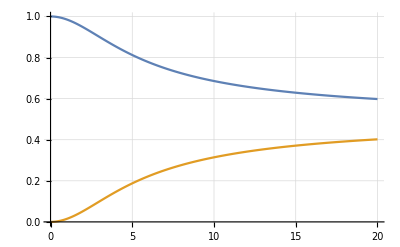

```mathematica
ListPlot[{C1ψ20bb[U],C1ψ20aa[U]},Joined->True,GridLines->Automatic]
```

```mathematica
Ket[ψ20]=S20(Ket[u,d]-Ket[d,u])+D02(Ket[ud,Subscript[0, 2]]+Ket[Subscript[0, 1],ud]);
Ket[ψ31]=S31(Ket[ud,u]+Ket[u,ud]);
Ket[ψ30]=S30(Ket[ud,u]-Ket[u,ud]);
Ket[ψ31p]=S31(Ket[ud,d]+Ket[d,ud]);
Ket[ψ30p]=S30(Ket[ud,d]-Ket[d,ud]);
ψ3=List[Ket[ψ30],Ket[ψ30p],Ket[ψ31],Ket[ψ31p]];
Ket[ψ11]=S11(Ket[u,Subscript[0, 2]]-Ket[Subscript[0, 1],u]);
Ket[ψ10]=S10(Ket[u,Subscript[0, 2]]+Ket[Subscript[0, 1],u]);
Ket[ψ11p]=S11(Ket[d,Subscript[0, 2]]-Ket[Subscript[0, 1],d]);
Ket[ψ10p]=S10(Ket[d,Subscript[0, 2]]+Ket[Subscript[0, 1],d]);
ψ1=List[Ket[ψ10],Ket[ψ10p],Ket[ψ11],Ket[ψ11p]];
ℰ3=List[ℰ30,ℰ30p,ℰ31,ℰ31p];
ℰ1=List[ℰ10,ℰ10p,ℰ11,ℰ11p];
G11uu2s2N = G1[ω,1,1,UP,Ket[ψ20],ψ3,ψ1,ℰ3,ℰ1,ℰ20,η]
```

(S10^2 (D02+S20)^2)/(ℰ10p-ℰ20-ⅈ η+ω)+(S11^2 (D02-S20)^2)/(ℰ11p-ℰ20-ⅈ η+ω)+((-D02-S20)^2 S30^2)/(ℰ20-ℰ30+ⅈ η+ω)+((D02-S20)^2 S31^2)/(ℰ20-ℰ31+ⅈ η+ω)

## Dimère asymétrique

### Vecteurs propres et valeurs propres N = 1

```mathematica
Ket[Subscript[0, 1],d]=nc[bz[[2,2,1]],v];
Ket[Subscript[0, 1],u]=nc[bz[[2,2,2]],v];
Ket[d,Subscript[0, 2]]=nc[bz[[2,2,3]],v];
Ket[u,Subscript[0, 2]]=nc[bz[[2,2,4]],v];
```

```mathematica
Ket[ψ10as]=1/N10as(Ket[u,Subscript[0, 2]]+(Δv/(2t)-ℰ10as/t)Ket[Subscript[0, 1],u]);
Ket[ψ10pas]=1/N10as(Ket[d,Subscript[0, 2]]+(Δv/(2t)-ℰ10as/t)Ket[Subscript[0, 1],d]);
Ket[ψ11as]=1/N11as(Ket[u,Subscript[0, 2]]+(Δv/(2t)-ℰ11as/t)Ket[Subscript[0, 1],u]);
Ket[ψ11pas]=1/N11as(Ket[d,Subscript[0, 2]]+(Δv/(2t)-ℰ11as/t)Ket[Subscript[0, 1],d]);
```

```mathematica
ℰ11as[t_,Δv_]:=√((Δv/2)^2+t^2)
ℰ10as[t_,Δv_]:=-√((Δv/2)^2+t^2)
```

```mathematica
ψ1as = List[Ket[ψ10as],Ket[ψ10pas],Ket[ψ11as],Ket[ψ11pas]];
ψ1asex = List[Ket[ψ11as],Ket[ψ11pas]];
```

```mathematica
ℰ1as:=List[ℰ10as,ℰ10as,ℰ11as,ℰ11as];
ℰ1asex:=List[ℰ11as,ℰ11as];
```

### Vecteurs propres et valeurs propres N = 2

```mathematica
Element[U,Reals]&&Element[𝒯,Reals];
```

```mathematica
Ket[Subscript[0, 1],ud]=nc[bz[[3,2,1]],v];
Ket[d,d]    =nc[bz[[3,2,2]],v];
Ket[d,u]    =nc[bz[[3,2,3]],v];
Ket[u,d]    =nc[bz[[3,2,4]],v];
Ket[u,u]    =nc[bz[[3,2,5]],v];
Ket[ud,Subscript[0, 2]]=nc[bz[[3,2,6]],v];
```

```mathematica
ℰ23as[𝒟_,U_]:=2/3*(U-Sqrt[U^2+12+3 𝒟^2]*Cos[1/3*ArcCos[(-(U^2+18-9 𝒟^2)*U)/((U^2+12+3 𝒟^2)^(3/2))]+π])
ℰ22as[𝒟_,U_]:=2/3*(U-Sqrt[U^2+12+3 𝒟^2]*Cos[1/3*ArcCos[(-(U^2+18-9 𝒟^2)*U)/((U^2+12+3 𝒟^2)^(3/2))]+π/3])
ℰ21as=0;
ℰ20as[𝒟_,U_]:=2/3*(U-Sqrt[U^2+12+3 𝒟^2]*Cos[1/3*ArcCos[(-(U^2+18-9 𝒟^2)*U)/((U^2+12+3 𝒟^2)^(3/2))]-π/3])
```

```mathematica
N20as[𝒟_,U_]:=Sqrt[2+(2/(U-𝒟-ℰ20as[𝒟,U]))^2+(2/(U+𝒟-ℰ20as[𝒟,U]))^2]
N22as[𝒟_,U_]:=Sqrt[2+(2/(U-𝒟-ℰ22as[𝒟,U]))^2+(2/(U+𝒟-ℰ22as[𝒟,U]))^2]
N23as[𝒟_,U_]:=Sqrt[2+(2/(U-𝒟-ℰ23as[𝒟,U]))^2+(2/(U+𝒟-ℰ23as[𝒟,U]))^2]
```

```mathematica
Ket[ψ23as]=1/N23as(Ket[u,d]-Ket[d,u]+(2t)/(U+Δv-ℰ23as)Ket[ud,Subscript[0, 2]]+(2t)/(U-Δv-ℰ23as)Ket[Subscript[0, 1],ud]);
Ket[ψ22as]=1/N22as(Ket[u,d]-Ket[d,u]+(2t)/(U+Δv-ℰ22as)Ket[ud,Subscript[0, 2]]+(2t)/(U-Δv-ℰ22as)Ket[Subscript[0, 1],ud]);
Ket[ψ21as]=1/Sqrt[2](Ket[u,d]+Ket[d,u]);
Ket[ψ20as]=1/N20as(Ket[u,d]-Ket[d,u]+(2t)/(U+Δv-ℰ20as)Ket[ud,Subscript[0, 2]]+(2t)/(U-Δv-ℰ20as)Ket[Subscript[0, 1],ud]);
```

```mathematica
ψ2as = List[Ket[ψ20as],Ket[ψ21as],Ket[ψ22as],Ket[ψ23as]];
ψ2asex = List[Ket[ψ21as],Ket[ψ22as],Ket[ψ23as]];
```

```mathematica
ℰ2as:=List[ℰ20as,ℰ21as,ℰ22as,ℰ23as];
ℰ2asex:=List[ℰ21as,ℰ22as,ℰ23as];
```

### Vecteurs propres et valeurs propres N = 3

```mathematica
Element[U,Reals]&&Element[𝒯,Reals];
```

```mathematica
Ket[d,ud]=nc[bz[[4,2,1]],v];
Ket[u,ud]=nc[bz[[4,2,2]],v];
Ket[ud,d]=nc[bz[[4,2,3]],v];
Ket[ud,u]=nc[bz[[4,2,4]],v];
```

```mathematica
N30as[𝒟_]:=Sqrt[1+1/4(𝒟+Sqrt[𝒟^2+4])^2]
N31as[𝒟_]:=Sqrt[1+1/4(-𝒟+Sqrt[𝒟^2+4])^2]
```

```mathematica
Ket[ψ31pas]=1/N31as(Ket[ud,d]+(-Δv/(2t)+√((Δv/(2t))^2+ 1))*Ket[d,ud]);
Ket[ψ31as]=1/N31as(Ket[ud,u]+(-Δv/(2t)+√((Δv/(2t))^2+ 1))*Ket[u,ud]);
Ket[ψ30pas]=1/N30as(Ket[ud,d]+(-Δv/(2t)-√((Δv/(2t))^2+ 1))*Ket[d,ud]);
Ket[ψ30as]=1/N30as(Ket[ud,u]+(-Δv/(2t)-√((Δv/(2t))^2+ 1))*Ket[u,ud]);
```

```mathematica
ℰ31as[𝒟_,U_]:=U+Sqrt[1+𝒟^2/4]
ℰ30as[𝒟_,U_]:=U-Sqrt[1+𝒟^2/4]
```

```mathematica
ψ3as = List[Ket[ψ30as],Ket[ψ30pas],Ket[ψ31as],Ket[ψ31pas]];
```

```mathematica
ℰ3as:=List[ℰ30as,ℰ30as,ℰ31as,ℰ31as];
```

```mathematica
G11uu2s2Nas = G1[ω,1,1,UP,Ket[ψ20as],ψ3as,ψ1as,ℰ3as,ℰ1as,ℰ20as,η]
```

(-ℰ10as/t+Δv/(2 t)+(2 t)/(U-ℰ20as+Δv))^2/(N10as^2 N20as^2 (ℰ10as-ℰ20as-ⅈ η+ω))+(-ℰ11as/t+Δv/(2 t)+(2 t)/(U-ℰ20as+Δv))^2/(N11as^2 N20as^2 (ℰ11as-ℰ20as-ⅈ η+ω))+((-1+(2 t (-Δv/(2 t)-Conjugate[√(1+Δv^2/(4 t^2))]))/(U-ℰ20as-Δv))^2)/(N20as^2 N30as^2 (ℰ20as-ℰ30as+ⅈ η+ω))+((-1+(2 t (-Δv/(2 t)+Conjugate[√(1+Δv^2/(4 t^2))]))/(U-ℰ20as-Δv))^2)/(N20as^2 N31as^2 (ℰ20as-ℰ31as+ⅈ η+ω))

```mathematica
G11dd2s2Nas =G1[ω,1,1,DO,Ket[ψ20as],ψ3as,ψ1as,ℰ3as,ℰ1as,ℰ20as,η]
```

(ℰ10as/t-Δv/(2 t)-(2 t)/(U-ℰ20as+Δv))^2/(N10as^2 N20as^2 (ℰ10as-ℰ20as-ⅈ η+ω))+(ℰ11as/t-Δv/(2 t)-(2 t)/(U-ℰ20as+Δv))^2/(N11as^2 N20as^2 (ℰ11as-ℰ20as-ⅈ η+ω))+((-1+(2 t (-Δv/(2 t)-Conjugate[√(1+Δv^2/(4 t^2))]))/(U-ℰ20as-Δv))^2)/(N20as^2 N30as^2 (ℰ20as-ℰ30as+ⅈ η+ω))+((-1+(2 t (-Δv/(2 t)+Conjugate[√(1+Δv^2/(4 t^2))]))/(U-ℰ20as-Δv))^2)/(N20as^2 N31as^2 (ℰ20as-ℰ31as+ⅈ η+ω))

```mathematica
G22uu2s2Nas =G1[ω,2,2,UP,Ket[ψ20as],ψ3as,ψ1as,ℰ3as,ℰ1as,ℰ20as,η]
```

(1+(2 t (-ℰ10as/t+Δv/(2 t)))/(U-ℰ20as-Δv))^2/(N10as^2 N20as^2 (ℰ10as-ℰ20as-ⅈ η+ω))+(1+(2 t (-ℰ11as/t+Δv/(2 t)))/(U-ℰ20as-Δv))^2/(N11as^2 N20as^2 (ℰ11as-ℰ20as-ⅈ η+ω))+((Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)-Conjugate[√(1+Δv^2/(4 t^2))])^2)/(N20as^2 N31as^2 (ℰ20as-ℰ31as+ⅈ η+ω))+((Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)+Conjugate[√(1+Δv^2/(4 t^2))])^2)/(N20as^2 N30as^2 (ℰ20as-ℰ30as+ⅈ η+ω))

```mathematica
G22dd2s2Nas =G1[ω,2,2,DO,Ket[ψ20as],ψ3as,ψ1as,ℰ3as,ℰ1as,ℰ20as,η]
```

(-1-(2 t (-ℰ10as/t+Δv/(2 t)))/(U-ℰ20as-Δv))^2/(N10as^2 N20as^2 (ℰ10as-ℰ20as-ⅈ η+ω))+(-1-(2 t (-ℰ11as/t+Δv/(2 t)))/(U-ℰ20as-Δv))^2/(N11as^2 N20as^2 (ℰ11as-ℰ20as-ⅈ η+ω))+((Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)-Conjugate[√(t^2+Δv^2/(4 t^2))])^2)/(N20as^2 N30as^2 (ℰ20as-ℰ30as+ⅈ η+ω))+((Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)+Conjugate[√(t^2+Δv^2/(4 t^2))])^2)/(N20as^2 N31as^2 (ℰ20as-ℰ31as+ⅈ η+ω))

```mathematica
G12uu2s2Nas = G1[ω,1,2,UP,Ket[ψ20as],ψ3as,ψ1as,ℰ3as,ℰ1as,ℰ20as,η]
```

((-ℰ10as/t+Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)) (1+(2 t (-ℰ10as/t+Δv/(2 t)))/(U-ℰ20as-Δv)))/(N10as^2 N20as^2 (ℰ10as-ℰ20as-ⅈ η+ω))+((-ℰ11as/t+Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)) (1+(2 t (-ℰ11as/t+Δv/(2 t)))/(U-ℰ20as-Δv)))/(N11as^2 N20as^2 (ℰ11as-ℰ20as-ⅈ η+ω))+((-1+(2 t (-Δv/(2 t)-Conjugate[√(1+Δv^2/(4 t^2))]))/(U-ℰ20as-Δv)) (Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)+Conjugate[√(1+Δv^2/(4 t^2))]))/(N20as^2 N30as^2 (ℰ20as-ℰ30as+ⅈ η+ω))+((Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)-Conjugate[√(1+Δv^2/(4 t^2))]) (-1+(2 t (-Δv/(2 t)+Conjugate[√(1+Δv^2/(4 t^2))]))/(U-ℰ20as-Δv)))/(N20as^2 N31as^2 (ℰ20as-ℰ31as+ⅈ η+ω))

```mathematica
G21uu2s2Nas = G1[ω,2,1,UP,Ket[ψ20as],ψ3as,ψ1as,ℰ3as,ℰ1as,ℰ20as,η]
```

((-ℰ10as/t+Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)) (1+(2 t (-ℰ10as/t+Δv/(2 t)))/(U-ℰ20as-Δv)))/(N10as^2 N20as^2 (ℰ10as-ℰ20as-ⅈ η+ω))+((-ℰ11as/t+Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)) (1+(2 t (-ℰ11as/t+Δv/(2 t)))/(U-ℰ20as-Δv)))/(N11as^2 N20as^2 (ℰ11as-ℰ20as-ⅈ η+ω))+((-1+(2 t (-Δv/(2 t)-Conjugate[√(1+Δv^2/(4 t^2))]))/(U-ℰ20as-Δv)) (Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)+Conjugate[√(1+Δv^2/(4 t^2))]))/(N20as^2 N30as^2 (ℰ20as-ℰ30as+ⅈ η+ω))+((Δv/(2 t)+(2 t)/(U-ℰ20as+Δv)-Conjugate[√(1+Δv^2/(4 t^2))]) (-1+(2 t (-Δv/(2 t)+Conjugate[√(1+Δv^2/(4 t^2))]))/(U-ℰ20as-Δv)))/(N20as^2 N31as^2 (ℰ20as-ℰ31as+ⅈ η+ω))

```mathematica
G12dd2s2Nas = G1[ω,1,2,DO,Ket[ψ20as],ψ3as,ψ1as,ℰ3as,ℰ1as,ℰ20as,η]
```

((ℰ10as/t-Δv/(2 t)-(2 t)/(U-ℰ20as+Δv)) (-1-(2 t (-ℰ10as/t+Δv/(2 t)))/(U-ℰ20as-Δv)))/(N10as^2 N20as^2 (ℰ10as-ℰ20as-ⅈ η+ω))+((ℰ11as/t-Δv/(2 t)-(2 t)/(U-ℰ20as+Δv)) (-1-(2 t (-ℰ11as/t+Δv/(2 t)))/(U-ℰ20as-Δv)))/(N11as^2 N20as^2 (ℰ11as-ℰ20as-ⅈ η+ω))

```mathematica
G11dd2s1Nas =G1[ω,1,1,DO,Ket[ψ10as],ψ2as,ψ0,ℰ2as,ℰ0,ℰ10as,η]
```

(ℰ10as/t-Δv/(2 t)-(2 t)/(U-ℰ20as+Δv))^2/(N10as^2 N20as^2 (ℰ10as-ℰ20as+ⅈ η+ω))+(-ℰ10as/t+Δv/(2 t))^2/(2 N10as^2 (ℰ10as-ℰ21as+ⅈ η+ω))+(ℰ10as/t-Δv/(2 t)-(2 t)/(U-ℰ22as+Δv))^2/(N10as^2 N22as^2 (ℰ10as-ℰ22as+ⅈ η+ω))+(ℰ10as/t-Δv/(2 t)-(2 t)/(U-ℰ23as+Δv))^2/(N10as^2 N23as^2 (ℰ10as-ℰ23as+ⅈ η+ω))

```mathematica
G12dd2s1Nas =G1[ω,1,2,DO,Ket[ψ10as],ψ2as[𝒟,U],ψ0,ℰ2as,ℰ0,ℰ10as,η]
```

-(Cos[ρ] Sin[ρ])/(2 (ℰ10as-ℰ21as+ⅈ η+ω))+((-(2 Cos[ρ])/(U+𝒟-ℰ20as)-Sin[ρ]) (-Cos[ρ]-(2 Sin[ρ])/(U-𝒟-ℰ20as)))/(N20as^2 (ℰ10as-ℰ20as+ⅈ η+ω))+((-(2 Cos[ρ])/(U+𝒟-ℰ22as)-Sin[ρ]) (-Cos[ρ]-(2 Sin[ρ])/(U-𝒟-ℰ22as)))/(N22as^2 (ℰ10as-ℰ22as+ⅈ η+ω))+((-(2 Cos[ρ])/(U+𝒟-ℰ23as)-Sin[ρ]) (-Cos[ρ]-(2 Sin[ρ])/(U-𝒟-ℰ23as)))/(N23as^2 (ℰ10as-ℰ23as+ⅈ η+ω))

```mathematica
G11uu2s1Nas =G1[ω,1,1,UP,Ket[ψ10as],ψ2as[𝒟,U],ψ0,ℰ2as,ℰ0,ℰ10as,η]
```

Cos[ρ]^2/(-ℰ10as-ⅈ η+ω)

```mathematica
G12uu2s1Nas =G1[ω,1,2,UP,Ket[ψ10as],ψ2as[𝒟,U],ψ0,ℰ2as,ℰ0,ℰ10as,η]
```

(Cos[ρ] Sin[ρ])/(-ℰ10as-ⅈ η+ω)

### Calcul de L2 exacte dimère asymétrique

```mathematica
G1111uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,1,1,1,1,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1112uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,1,1,1,2,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1121uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,1,1,2,1,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1122uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,1,1,2,2,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
```

```mathematica
G1211uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,1,2,1,1,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1212uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,1,2,1,2,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1221uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,1,2,2,1,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1222uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,1,2,2,2,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
```

```mathematica
G2111uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,2,1,1,1,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2112uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,2,1,1,2,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2121uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,2,1,2,1,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2122uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,2,1,2,2,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
```

```mathematica
G2211uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,2,2,1,1,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2212uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,2,2,1,2,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2221uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,2,2,2,1,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2222uuuuas[ω_,𝒟_,U_,η_] :=G2[ω,2,2,2,2,UP,UP,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
G1111uuddas[ω_,𝒟_,U_,η_] :=G2[ω,1,1,1,1,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1112uuddas[ω_,𝒟_,U_,η_] :=G2[ω,1,1,1,2,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1121uuddas[ω_,𝒟_,U_,η_] :=G2[ω,1,1,2,1,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1122uuddas[ω_,𝒟_,U_,η_] :=G2[ω,1,1,2,2,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
```

```mathematica
G1211uuddas[ω_,𝒟_,U_,η_] :=G2[ω,1,2,1,1,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1212uuddas[ω_,𝒟_,U_,η_] :=G2[ω,1,2,1,2,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1221uuddas[ω_,𝒟_,U_,η_] :=G2[ω,1,2,2,1,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G1222uuddas[ω_,𝒟_,U_,η_] :=G2[ω,1,2,2,2,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
```

```mathematica
G2111uuddas[ω_,𝒟_,U_,η_] :=G2[ω,2,1,1,1,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2112uuddas[ω_,𝒟_,U_,η_] :=G2[ω,2,1,1,2,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2121uuddas[ω_,𝒟_,U_,η_] :=G2[ω,2,1,2,1,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2122uuddas[ω_,𝒟_,U_,η_] :=G2[ω,2,1,2,2,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
```

```mathematica
G2211uuddas[ω_,𝒟_,U_,η_] :=G2[ω,2,2,1,1,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2212uuddas[ω_,𝒟_,U_,η_] :=G2[ω,2,2,1,2,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2221uuddas[ω_,𝒟_,U_,η_] :=G2[ω,2,2,2,1,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
G2222uuddas[ω_,𝒟_,U_,η_] :=G2[ω,2,2,2,2,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
```

```mathematica
G2[ω,1,1,2,1,UP,DO,Ket[ψ20as[𝒟,U]],ψ2asex[𝒟,U],ℰ2asex,ℰ20as,η]
```

-1/(N20as^2 (U+𝒟-ℰ20as) (-ℰ20as+ℰ21as-ⅈ η+ω))-(2 (1/(U+𝒟-ℰ20as)+1/(U-𝒟-ℰ22as)) (1+4/((U+𝒟-ℰ20as) (U+𝒟-ℰ22as))))/(N20as^2 N22as^2 (-ℰ20as+ℰ22as-ⅈ η+ω))-(2 (1/(U+𝒟-ℰ20as)+1/(U-𝒟-ℰ23as)) (1+4/((U+𝒟-ℰ20as) (U+𝒟-ℰ23as))))/(N20as^2 N23as^2 (-ℰ20as+ℰ23as-ⅈ η+ω))+1/(N20as^2 (-U+𝒟+ℰ20as) (ℰ20as-ℰ21as+ⅈ η+ω))+(2 (1/(U-𝒟-ℰ20as)+1/(U+𝒟-ℰ22as)) (1+4/((U+𝒟-ℰ20as) (U+𝒟-ℰ22as))))/(N20as^2 N22as^2 (ℰ20as-ℰ22as+ⅈ η+ω))+(2 (1/(U-𝒟-ℰ20as)+1/(U+𝒟-ℰ23as)) (1+4/((U+𝒟-ℰ20as) (U+𝒟-ℰ23as))))/(N20as^2 N23as^2 (ℰ20as-ℰ23as+ⅈ η+ω))